```mathematica
ClearAll["Global`*"]
```

```mathematica
H=({{0, b1/2, 0, 0, 0, 0, 0, 0}, {b1/2, -AN-AC, 0, 0, 0, 0, 0, 0}, {0, 0, 0, b1/2, 0, 0, 0, 0}, {0, 0, b1/2, -AN, 0, 0, 0, 0}, {0, 0, 0, 0, 0, b1/2, 0, 0}, {0, 0, 0, 0, b1/2, -AC, 0, 0}, {0, 0, 0, 0, 0, 0, 0, b1/2}, {0, 0, 0, 0, 0, 0, b1/2, 0}});
```

```mathematica
U=MatrixExp[-ⅈ*t*H]//FullSimplify;
U//MatrixForm;
```

```mathematica
Uc1=U/.t->myn*π/b1//FullSimplify;
Uc1//MatrixForm;
```

```mathematica
Rz1=({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, ((-1)^myn)*-ⅈ, 0}, {0, 0, 0, 0, 0, 0, 0, ((-1)^myn)*-ⅈ}});
Uc2=Rz1.Uc1//FullSimplify;
```

```mathematica
Uc2//MatrixForm;
Rz2=({{((-1)^l)*ⅇ^(-(ⅈ (AC+AN) myn π)/(2 b1)), 0, 0, 0, 0, 0, 0, 0}, {0, ((-1)^l)*ⅇ^(-(ⅈ (AC+AN)myn π)/(2 b1)), 0, 0, 0, 0, 0, 0}, {0, 0, ((-1)^k)*ⅇ^(-(ⅈ AN myn π)/(2 b1)), 0, 0, 0, 0, 0}, {0, 0, 0, ((-1)^k)*ⅇ^(-(ⅈ AN myn π)/(2 b1)), 0, 0, 0, 0}, {0, 0, 0, 0, ((-1)^m)*ⅇ^(-(ⅈ AC myn π)/(2 b1)), 0, 0, 0}, {0, 0, 0, 0, 0, ((-1)^m)*ⅇ^(-(ⅈ AC myn π)/(2 b1)), 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1}});
```

```mathematica
Uc3=Rz2.Uc2 //FullSimplify;
Uc3 // MatrixForm;
```

```mathematica
Ucnot=({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 1, 0}});
Fav=(Abs[Tr[Ucnot.Uc3]]^2+8)/72//FullSimplify//ComplexExpand;
```

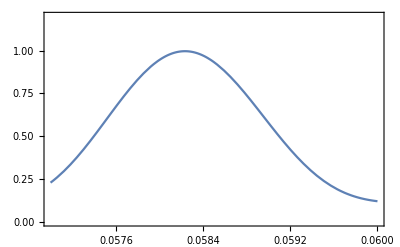

```mathematica
Fav1=Fav/.{AN->3.03,AC->(3.03*0.0753),myn->1,k->26,l->28,m->2};
Plot[Fav1,{b1,0.057,0.060},PlotRange->{0,1.2},Frame->True] 
localMax1=FindMaximum[{Fav1,0.057<=b1<=0.060},{b1,0.058}]
```

```mathematica
{0.9970872183327251,{b1->0.05823372833728373}}
tgnew[b1_,n_]:= n/(b1*Sqrt[2])
tgnew[localMax1[[2]][[1]][[2]],1]
```

{0.997087,{b1→0.0582337}}

12.1426

```mathematica
tgnew[0.09466996169905253,1]
```

7.46918

```mathematica
(*Extracted Values:
ratio 0.42811, {0.9995212333099991,{b1->0.10824970928351745},14.,20.,6., tg 6.532181803228311,
ratio 0.53795, {0.9996571107199458,{b1->0.11657531503952925}, 13.,20.,7., tg 6.065664767423328,
ratio 0.05400, {0.9881110912440264,{b1->0.08894530793584615}, 17.,18.,1., tg 7.949905369899494,
ratio 0.11511,{0.9970485414056626,{b1->0.08904519644722907}17,19,2 , tg 7.940987379432656,
ratio 0.2487, {0.9992115824056094,{b1->0.09466996169905253}16,20,4, tg 7.4691778521510095,
ratio 0.0753,{0.9970872183327251,{b1->0.05823372833728373}tg 12.142564135530842,,26,28,2)
```